# Wolfram语言专题讲座 机器学习和人工智能

杨圣汇 Wolfram Research Inc

-Graphics-

## 提纲

### 神经网络发展历史

发展回顾

### 神经网络在Wolfram语言中的应用

图像处理

文本处理

声音处理

### 神经网络的基本结构

什么是神经网络

Wolfram语言中的神经网络架构

Wolfram 神经网络资源库

### Wolfram U

60分钟零基础入门

重新训练

网络层

更改和检查神经网络

更多资源

### 自己搭建神经网络

从零搭建神经网络

使用已有架构

剖析神经网络

## 神经网络发展编年史

1942--第一个可计算神经网络诞生

1965--第一个可用的多层神经网络

1975--逆向传递算法用于训练多层神经网络

1990s--受限于数据和算力，别的机器学习算法更具优势

2005-2007-- 可使用更深层的网络进行无监督学习; 使用GPU加速

2009--ImageNet: 一千四百万张图片和两万一千种类别构成的图片数据库 (Original paper)

2012--AlexNet: 2012年大规模视觉识别挑战赛的冠军 (Original paper)

2015--Wolfram 博客 https://writings.stephenwolfram.com/2015/05/wolfram-language-artificial-intelligence-the-image-identification-project/

- 源自 The data that transformed AI research—and possibly the world by Dave Gershgorn

## Wolfram语言中的神经网络应用

### Image Identification 项目

ImageIdentify 与 网页版图片识别器

```mathematica
ImageIdentify[-Graphics-]
```

giant anteater

```mathematica
ImageIdentify[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{space station,earth,ballistic capsule,sun}

```mathematica
ImageIdentify[-Graphics-](*Image Source: https://commons.wikimedia.org/wiki/File:Retrato_del_Maestro_Yoda.jpg*)
```

Yoda

```mathematica
Import["https://commons.wikimedia.org/wiki/Commons:Featured_pictures#Animals","Images"][[1;;5]]
```

```mathematica
ImageIdentify/@ %
```

## 神经网络在图像处理方面的应用

```mathematica
ImageContents[-Graphics-]
```

```mathematica
ImageContainsQ[-Graphics-,Entity["Species","Family:Elephantidae"]]
```

True

```mathematica
ImageInstanceQ[-Graphics-,Entity["Species","Species:FelisCatus"]]
```

True

```mathematica
ImageCases[-Graphics-]
```

<|domestic cat→{-Graphics-},domestic dog→{-Graphics-}|>

```mathematica
FindFaces[-Graphics-]
```

{Rectangle[{237.5,135.5},{273.5,181.5}],Rectangle[{154.5,140.5},{191.5,194.5}],Rectangle[{45.5,155.5},{82.5,205.5}],Rectangle[{326.5,120.5},{365.5,168.5}]}

```mathematica
HighlightImage[-Graphics-,FindFaces[#,"BoundingBox"]&]
```

-Graphics-

```mathematica
FacialFeatures[-Graphics-]//Dataset
```

```mathematica
NetModel["CycleGAN Photo-to-Cezanne Translation"]
```

```mathematica
ImageRestyle[-Graphics-,-Graphics-]
```

## 神经网络在文本处理中的应用

```mathematica
FindTextualAnswer["Paris is the capital and most populous city of France, with a 2015 population of 2,229,621.",{"How many people live in Paris?","In which country is Paris?"},1,{"String","Position"}]
```

{{{2,229,621,{82,90}}},{{France,{48,53}}}}

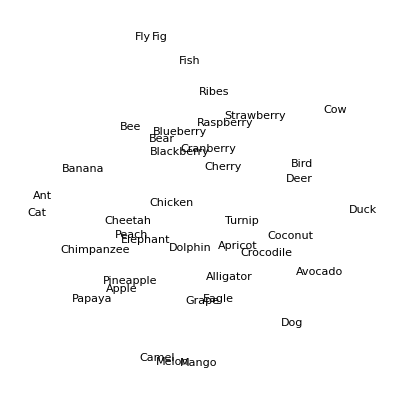

```mathematica
animals={"Alligator","Ant","Bear","Bee","Bird","Camel","Cat","Cheetah","Chicken","Chimpanzee","Cow","Crocodile","Deer","Dog","Dolphin","Duck","Eagle","Elephant","Fish","Fly"};
fruits={"Apple","Apricot","Avocado","Banana","Blackberry","Blueberry","Cherry","Coconut","Cranberry","Grape","Turnip","Mango","Melon","Papaya","Peach","Pineapple","Raspberry","Strawberry","Ribes","Fig"};
FeatureSpacePlot[Join[animals,fruits]]
```

```mathematica
Information@NetModel["GloVe 100-Dimensional Word Vectors Trained on Tweets"]
```

Net Information

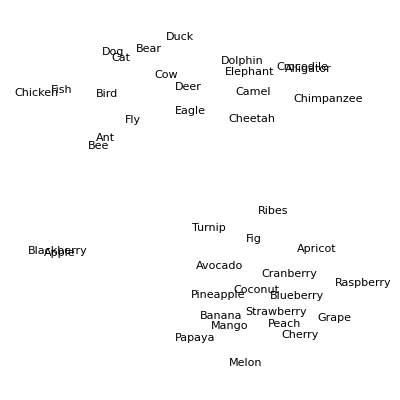

```mathematica
FeatureSpacePlot[Join[animals,fruits],FeatureExtractor->NetModel["GloVe 100-Dimensional Word Vectors Trained on Tweets"]]
```

## 神经网络在音频处理中的应用

```mathematica
SpeechRecognize[AudioCapture[]]
```

a one two three four five

```mathematica
SpeechCases[AudioCapture[],"Noun"]
```

{car}

```mathematica
AudioIdentify[AudioCapture[]]
```

chirp

## 神经网络

什么是神经网络

由人脑结构启发

从案例中学习: images, audio, text, numbers

神经网络的学习过程是把输入数据转化为数值然后转码，映射到不同的类型的对象上

基本元素

编码/Encoders 以及 解码/decoders: 把输入数据变化为数值张量

神经网络的层/Layers: 对张量进行操作

容器Containers: 把以上所有操作进行封装

激活函数和损失函数

CPU/GPU 硬件选项

通过学习来训练神经网络 =
利用随机梯度下降法和反向传递法来优化所有的参数/stochastic gradient descent and back propagation

## Wolfram 神经网络库

不断扩展深度学习神经网络案例可以快速部署，或者进行迁移学习

跨平台使用其他架构 (例如 Caffe, Torch, MXNet, TensorFlow, 等) 产生的网络

Wolfram研究公司专业的数据集和相应的经过训练的神经网络

下载神经网络

```mathematica
NetModel["Wolfram ImageIdentify Net V1"]
```

使用该网络进行图像识别

```mathematica
pred=NetModel["Wolfram ImageIdentify Net V1"][-Graphics-]
```

结果对象里的各种属性

```mathematica
pred["Definition"]
```

```mathematica
pred["Properties"]
```

选取概率最高的十个预测

```mathematica
NetModel["Wolfram ImageIdentify Net V1"][-Graphics-,{"TopProbabilities",10}]
```

{laser→1.69539×10^-6,brain coral→1.90332×10^-6,reef→2.24776×10^-6,sea feather→2.34097×10^-6,umbrella→8.65469×10^-6,mushroom coral→0.00003948,peahen→0.0265315,peacock→0.20057,green peafowl→0.362713,blue peafowl→0.410115}

```mathematica
Entity["Concept","BluePeafowl::8h39h"]["Image"]
```

-Graphics-

检查不在训练集里面出现的物体

```mathematica
NetModel["Wolfram ImageIdentify Net V1"][-Graphics-]
```

power cord

## 零基础人工智能入门课程

关键信息: 神经网络可以表示为符号图形，其中每个层都保存有关层类型、输入和输出以及可训练权重的固定信息

### 重新训练

```mathematica
net=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
net[-Graphics-]
```

0

```mathematica
new=NetTrain[net,{-Graphics-->1},TargetDevice->"GPU"]
```

NetChain[<>]

```mathematica
net[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{3,9,8,4}

```mathematica
new@-Graphics-
```

1

```mathematica
trainingData=ResourceData["MNIST","TrainingData"];
testData=ResourceData["MNIST","TestData"];
```

```mathematica
RandomSample[trainingData,5]
```

{-Graphics-→0,-Graphics-→0,-Graphics-→5,-Graphics-→4,-Graphics-→3}

```mathematica
NetModel["LeNet"]
```

NetChain[<>]

```mathematica
myNet = NetTrain[NetModel["LeNet"],trainingData,ValidationSet->testData,TargetDevice->"GPU"]
```

NetChain[<>]

```mathematica
myNet[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{3,9,8,4}

```mathematica
Options[NeuralNetworks`ToNetTrainer]
```

{BatchSize→Automatic,MaxBatchSize→None,Context→1,Optimizer→ADAM,TotalBatches→4096,LearningRateMultipliers→Automatic,TrainingUpdateSchedule→Automatic,UpdatesPerBatch→1,GradientScale→1,DataType→0,MixedPrecisionQ→False,Validation→True,Measurements→{},ErrorHandler→Automatic}

### 层

```mathematica
net
```

```mathematica
layer=NetExtract[net,-1]
```

SoftmaxLayer[<>]

将归一化指数函数/softmax function 作用于一个列表

```mathematica
layer[{1,2,5,2,4,7,4,3,5,3}]
```

{0.00174213,0.00473559,0.0951169,0.00473559,0.0349916,0.702824,0.0349916,0.0128727,0.0951169,0.0128727}

和直接用定义求解一致

```mathematica
Exp[1.]/Total[Exp[{1,2,5,2,4,7,4,3,5,3}]]
```

0.00174213

内置支持的神经网络层

```mathematica
?*Layer
```

点击上面任意一个符号

### 更改和检视神经网络

Wolfram语言中符号化表示的神经网络和一般列表数据对象相似

```mathematica
net=NetModel["Wolfram ImageIdentify Net for WL 11.1"]
```

NetChain[<>]

```mathematica
net[-Graphics-]
```

tiger

```mathematica
Take[net,5]
```

NetChain[<>]

```mathematica
Image/@Take[net,10][-Graphics-]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Image/@Take[net,10][-Graphics-]
```

https://medium.com/@pallawi.ds/ai-starter-build-your-first-convolution-neural-network-in-keras-from-scratch-to-perform-a059eaa6d4ff

## 调试网络

由科幻小说和喜剧电影旧电影海报构成的训练和测试集合

```mathematica
training={-Graphics-->"ScienceFiction",-Graphics-->"ScienceFiction",-Graphics-->"ScienceFiction",-Graphics-->"ScienceFiction",-Graphics-->"ScienceFiction",-Graphics-->"ScienceFiction",-Graphics-->"ScienceFiction",-Graphics-->"ScienceFiction",-Graphics-->"Comedy",-Graphics-->"Comedy",-Graphics-->"Comedy",-Graphics-->"Comedy",-Graphics-->"Comedy",-Graphics-->"Comedy",-Graphics-->"Comedy",-Graphics-->"Comedy"};testset={-Graphics-->"ScienceFiction",-Graphics-->"ScienceFiction",-Graphics-->"Comedy",-Graphics-->"Comedy"};
```

下载预训练网络

```mathematica
net=NetModel["Wolfram ImageIdentify Net V1"]
```

去除最后两层

```mathematica
changedNet=NetDrop[net,-2]
```

加上两层新的自定义层

```mathematica
newNet=NetJoin[changedNet,NetChain[Association["classifier"->LinearLayer[],"probabilities"->SoftmaxLayer[]],"Output"->NetDecoder[{"Class",{"ScienceFiction","Comedy"}}]]]
```

根据培训数据培训新网络

```mathematica
trainedNet=NetTrain[newNet,training,LearningRateMultipliers->{"classifier"->1,_->0}]
```

数据测试

{-Graphics-→ScienceFiction,-Graphics-→ScienceFiction,-Graphics-→Comedy,-Graphics-→Comedy}

```mathematica
trainedNet[Keys[testset]]
```

## 参考链接

An AI Pioneer Explains the Evolution of Neural Networks

What Is a Neural Net Exactly?— Wolfram 外联部门

Neural Networks: An Introduction—Wolfram博客

Neural networks in the Wolfram Language—tutorial

Wolfram Neural Net Repository

Launching the Wolfram Neural Net Repository—Wolfram博客

Tech Note: Introduction to Neural Nets

Collection of tutorials: Neural Networks in the Wolfram Language

Blog post: Neural Networks: An Introduction